```mathematica
(* create a list of random x and y velocities *)
vx={};
vy={};
i=1;
particles=25;
Do[vxtest=RandomReal[]-0.5;AppendTo[vx,vxtest];vytest=RandomReal[]-0.5;
AppendTo[vy,vytest],{i,1,particles,+i}];

(* set the total velocity to zero *)
vxdifference=Sum[vx[[i]],{i,1,particles,+i}]/particles;
vydifference=Sum[vy[[i]],{i,1,particles,+i}]/particles;
Do[vx[[i]]=vx[[i]]-vxdifference,{i,1,particles,+i}];
Do[vy[[i]]=vy[[i]]-vydifference,{i,1,particles,+i}];

(* rescale the velocities to the desired kinetic energy *)
InitialEnergy = 0.00836 *300; (* assuming approximately room temp, and new units of energy where 1 energy = 1.65*10^(-21) J  *)
vsquared = 0.0;
Do[vsquared =vsquared+ vx[[i]]*vx[[i]]+vy[[i]]*vy[[i]],{i,1,particles,+i}]
kineticEnergyPerParticle=0.5*vsquared/particles; (* remember mass = 1 unit = 6.69*10^(-26) kg *)
rescale = Sqrt[InitialEnergy/kineticEnergyPerParticle];
Do[vx[[i]]=vx[[i]]*rescale,{i,1,particles,+i}];
Do[vy[[i]]=vy[[i]]*rescale,{i,1,particles,+i}];
vsquared=0.0;
Do[vsquared =vsquared+ vx[[i]]*vx[[i]]+vy[[i]]*vy[[i]],{i,1,particles,+i}]
origVX = vx
origVY = vy
```

{0.149626,-0.285271,-2.58194,1.32749,-2.67884,1.86855,-2.32,-2.41995,0.802248,1.16177,0.109419,-0.285408,0.0379759,1.55648,1.46427,2.29332,1.65912,0.0149387,-0.847218,-0.980735,0.93771,2.10389,0.186555,-2.5701,-0.703904}

{-2.09667,1.70837,-1.08464,-1.7362,-0.0162169,-1.40957,1.48023,1.50298,-2.13087,2.69129,0.308425,0.0763829,-2.08622,2.75565,-0.337872,2.16684,0.725525,-1.57863,-1.96164,2.05912,0.955669,-0.435614,-2.24326,-0.684439,1.37137}

```mathematica
(* set initial positions *)
```

{{{1,1},{1,3},{1,5},{1,7},{1,9},{3,1},{3,3},{3,5},{3,7},{3,9},{5,1},{5,3},{5,5},{5,7},{5,9},{7,1},{7,3},{7,5},{7,7},{7,9},{9,1},{9,3},{9,5},{9,7},{9,9}}}

{{{1,1},{1,3},{1,5},{1,7},{1,9},{3,1},{3,3},{3,5},{3,7},{3,9},{5,1},{5,3},{5,5},{5,7},{5,9},{7,1},{7,3},{7,5},{7,7},{7,9},{9,1},{9,3},{9,5},{9,7},{9,9}}}

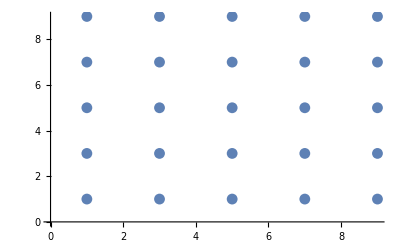

{1,1,1,1,1,3,3,3,3,3,5,5,5,5,5,7,7,7,7,7,9,9,9,9,9}

{1,3,5,7,9,1,3,5,7,9,1,3,5,7,9,1,3,5,7,9,1,3,5,7,9}

```mathematica
spacing = 10/Sqrt[particles];
startzero= spacing/2;
startx=startzero;
starty=startzero;
positionx={};
positiony={};
i=1;
Do[positionxtest=startx;
starty=startzero;
j=1;
Do[positionytest=starty;AppendTo[positionx,positionxtest];
AppendTo[positiony,positionytest];starty=starty+spacing,{j,1,Sqrt[particles],+j}];
startx=startx+spacing, {i,1,Sqrt[particles],+i}]
particleposition={};
i=1;
Do[
particleposition= AppendTo[particleposition,{positionx[[i]],positiony[[i]]}],
{i,1,particles}]
data={};
data={particleposition}
basicData = {particleposition}
ListPlot[particleposition]
origPositionx = positionx
origPositiony = positiony
```

```mathematica
(* intial conditions positionx, positiony, vx, vy *)
(* calculate acceleration in x and acceleration in y for all particles *)
ax={};ay={};
Do[
axx=0;ayy=0; 
Do[If[i!=j,
rx=positionx[[i]]-positionx[[j]]+.00000000000001;
ry=positiony[[i]]-positiony[[j]]+.00000000000001;
r=Sqrt[rx^2+ry^2];
theta=ArcTan[ry/rx];
axx=axx+(4*((12/r^13)-(6/r^7)))*Cos[theta]*(-1)*Sign[rx];
ayy=ayy +(4*((12/r^13)-(6/r^7)))*Abs[Sin[theta]]*Sign[ry]*(-1)],
{i,1,25}];
ax=AppendTo[ax,axx];
ay=AppendTo[ay,ayy],
{j,1,particles}]
origAX = ax 
origAY = ay
```

{0.196002,0.208333,0.20871,0.208333,0.196002,0.00233947,0.00299178,0.00308454,0.00299178,0.00233947,-1.20859×10^-14,-1.15543×10^-14,-1.15421×10^-14,-1.15488×10^-14,-1.20325×10^-14,-0.00233947,-0.00299178,-0.00308454,-0.00299178,-0.00233947,-0.196002,-0.208333,-0.20871,-0.208333,-0.196002}

{0.196002,0.00233947,-1.20294×10^-14,-0.00233947,-0.196002,0.208333,0.00299178,-1.14743×10^-14,-0.00299178,-0.208333,0.20871,0.00308454,-1.14744×10^-14,-0.00308454,-0.20871,0.208333,0.00299178,-1.14751×10^-14,-0.00299178,-0.208333,0.196002,0.00233947,-1.20156×10^-14,-0.00233947,-0.196002}

```mathematica
(* recursion relationship for one particle *)
positionx = origPositionx;
positiony = origPositiony;
vx = origVX;
vy = origVY;
ax = origAX;
ay = origAY;
timestep=0.01;
t = 0;
tmax = 100; 
(* verlet algorithm *)

i = 1;
j = 1;
positionPlus = {};
resultant= {};

While [ t< tmax,
	While [ i≤particles, 	
	positionxplus= positionx[[i]]+vx[[i]]*timestep+1/2*ax[[i]]*timestep^2;
	ax1 = -4*(-(12/positionxplus^13)+(6/positionxplus^7));
	vx1 = vx[[i]]+1/2*(ax1+ax[[i]])*timestep;
	positionyplus= positiony[[i]]+vy[[i]]*timestep+1/2*ay[[i]]*timestep^2;
	ayplus = -4*(-(12/positionyplus^13)+(6/positionyplus^7));
	vyplus = vy[[i]]+1/2*(ayplus+ay[[i]])*timestep;
	(*Print[positionxplus];
	Print[i];*)
	If [ (positionxplus≤  0 ∨ positionxplus≥  10),  
		vx = ReplacePart[vx, i ->-vx[[i]]/(√3)] (* vy[[i]]/3,     *) ;
		positionxplus= positionx[[i]]+vx[[i]]*timestep+1/2*ax[[i]]*timestep^2,

		vx = ReplacePart[vx, i -> vx1];
		];


	positionx = ReplacePart[positionx, i-> positionxplus];

	If [ (positionyplus≤ 0 ∨ positionyplus≥  10),  
		vy = ReplacePart[vy, i -> -vy[[i]]/(√3)]; (* √(((2*0.00836 *300)*293)/1) *) (* √((kineticEnergyPerParticle*293)/1) *) 
		positionyplus= positiony[[i]]+vy[[i]]*timestep+1/2*ay[[i]]*timestep^2,
		vy = ReplacePart[vy, i -> vyplus];
		];

	
	positiony = ReplacePart[positiony, i-> positionyplus];
	positionPlus = AppendTo [positionPlus,{positionxplus,positionyplus}]; 

	
	ax = ReplacePart[ax, i -> ax1];
	(*Print[i];
	Print[ax1];	
	Print[ax];*)
	ay = ReplacePart[ay, i-> ayplus];
	(*Print[ayplus];
	Print[ay];*)
	i++;
	];
i = 1; 
resultant = AppendTo[resultant, positionPlus];
(*Print[positionx];
Print[positiony];*)
posXPlus = {};
posYPlus = {};
positionPlus = {};
 t = t+ timestep; 
]
resultant
positiony;
positionx;
```

{{{1.00151,0.979043},{0.997158,3.01708},{0.974191,4.98915},{1.01329,6.98264},{0.973221,8.99983},{3.01869,0.985915},{2.9768,3.0148},12,{6.99019,9.02058},{9.00937,1.00957},{9.02103,2.99564},{9.00186,4.97757},{8.97429,6.99316},{8.99295,9.0137}},9998,{1}}
 |  |  |  |

{{1.00151,0.979043},{0.997158,3.01708},{0.974191,4.98915},{1.01329,6.98264},{0.973221,8.99983},{3.01869,0.985915},{2.9768,3.0148},{2.9758,5.01503},{3.00802,6.97869},{3.01162,9.0269},{5.00109,1.00309},{4.99715,3.00076},{5.00038,4.97914},{5.01556,7.02756},{5.01464,8.99661},{7.02293,1.02168},{7.01659,3.00726},{7.00015,4.98421},{6.99153,6.98038},{6.99019,9.02058},{9.00937,1.00957},{9.02103,2.99564},{9.00186,4.97757},{8.97429,6.99316},{8.99295,9.0137}}

{{1.29003,1.406},{1.27779,3.42685},{1.47243,4.72883},{1.42326,6.56595},{1.48675,8.9957},{3.46691,1.33059},{2.41943,3.36981},{2.39443,5.37574},{3.20028,6.46728},{3.29018,9.67256},{5.02735,1.29974},{4.92864,3.01878},{5.00948,4.47843},{5.38911,7.68891},{5.36606,8.91527},{7.57333,1.58194},{7.41477,3.1811},{7.00373,4.60533},{6.78819,6.50959},{6.75481,9.51452},{9.23418,1.36708},{9.52571,2.89074},{9.04638,4.43917},{8.35722,6.82889},{8.82378,9.3426}}

{{2.01297,4.21086},{2.14299,5.55892},{4.87487,3.37206},{3.00963,4.39557},{5.00936,8.9742},{5.79944,3.31014},{2.40604,5.2163},{2.53732,7.25431},{4.19739,3.80348},{4.73786,8.24026},{5.16381,2.04648},{4.57146,3.10334},{5.05663,1.86293},{7.33457,9.30787},{7.19624,8.49162},{9.71648,4.16787},{9.48864,4.08197},{7.02235,2.62986},{5.7291,4.05737},{5.52882,8.77588},{9.75497,2.55878},{8.73784,2.3235},{9.27826,1.6219},{5.14327,5.97328},{7.94267,9.36955}}

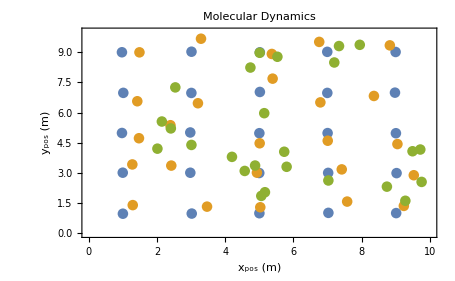

```mathematica
(* prepare data for plotting *)
resultant[[1]]
resultant[[25]]
resultant[[150]]
ListPlot[{resultant[[1]],resultant[[25]], resultant[[150]]},PlotLabel -> (" Molecular Dynamics"),Frame->True,FrameLabel->{"x_pos (m) ","y_pos (m)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotRange->{{0,10},{0,10}}]
(*
data = basicData;
particleposition={};
Do[
particleposition=AppendTo[particleposition,{posXPlus[[i]],posYPlus[[i]]}],
{i,1,particles}]
data=AppendTo[data,particleposition];
particleposition;
data;
p1 = ListPlot[data,PlotLabel -> (" Movement of Particles"),PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"x (m) ","y (m)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotStyle->{RGBColor[0,0,0],PointSize[0.01]},AspectRatio->1];
p2 = ListPlot[particleposition,PlotLabel -> (" Movement of Particles"),PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"x (m) ","y (m)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotStyle->{RGBColor[0,0,0],PointSize[0.01]},AspectRatio->1];
p3 = ListPlot[basicData,PlotLabel -> (" Movement of Particles"),PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"x (m) ","y (m)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotStyle->{RGBColor[0,0,0],PointSize[0.01]},AspectRatio->1];
*)
```

```mathematica
line=List[{10,0},{10,10}];
line1=List[{0,0},{10,0}];
line2=List[{0,0},{0,10}];
line3 = List[{0,10},{10,10}];
Animate[ListPlot[{resultant[[i]],line,line1,line2,line3},Joined->{False,True, True, True, True}, PlotStyle->{Blue,Black,Black, Black,Black} , Axes->False;PlotRange->{{0,12},{0,12}}],{i,1,tmax/timestep,1}, AnimationRunning->True]
```

```mathematica
length = 3.4 *10^-10;
energy = 1.65 *10^-21;
Clear[radius];
lenardJones = 4*energy*((length/radius)^12- (length/radius)^6)
force = -1* D[lenardJones,radius]
radius = 1;
force
acc = force/ ( 6.69*10^-26)
```

6.6×10^-21 ((2.38642×10^-114)/radius^12-(1.5448×10^-57)/radius^6)

-6.6×10^-21 (-(2.8637×10^-113)/radius^13+(9.26883×10^-57)/radius^7)

-6.11743×10^-77

-9.14413×10^-52

3.001×10^-11

2.95188×10^-8

General::ivar: 3.001×10^-11 is not a valid variable.

-∂_(3.001×10^-11) 2.95188×10^-8

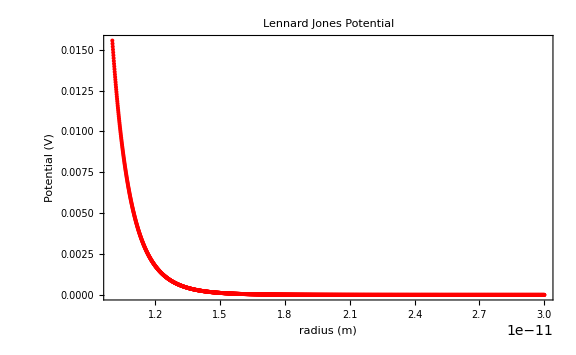

```mathematica
myData = List[];
AppendTo[myData, {radius, lenardJones}]; 


radius = 0.1*10^-10; 
While [radius<3*10^-11,
			radius = radius + 0.0001*10^-10;
			lenardJones = 4*energy*((length/radius)^12- (length/radius)^6);
			AppendTo[myData,{radius, lenardJones}];

			i++; 
]
myData;

ListPlot[myData,PlotLabel -> (" Lennard Jones Potential"),PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"radius (m) ","Potential (V)","",""},LabelStyle->(FontSize->14), PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
```

4 (-12/r^13+6/r^7)

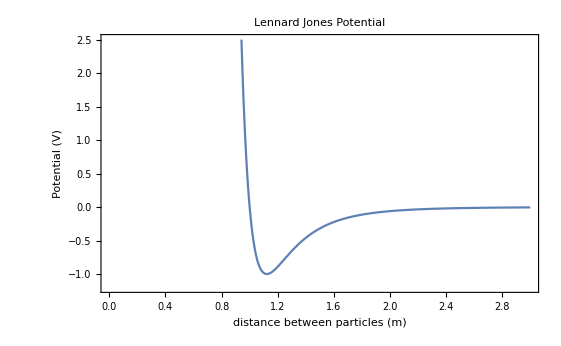

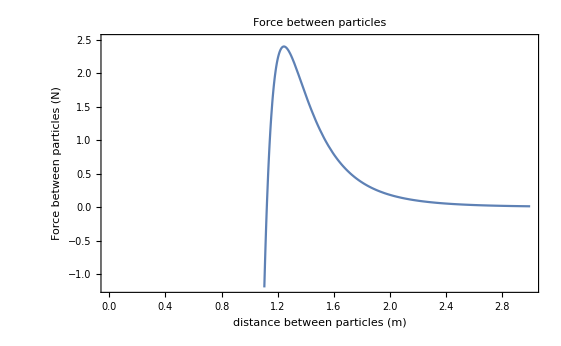

```mathematica
lenardJones =4 (1/r^12-1/r^6);
force = D[lenardJones,r]
Plot[lenardJones,{r,0.001,3},Frame->True,LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotRange->{-1.2,2.5}, PlotLabel-> "Lennard Jones Potential", FrameLabel->{"distance between particles (m) ","Potential (V)","",""}]
Plot[force,{r,0.001,3},Frame->True,LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotRange->{-1.2,2.5}, PlotLabel-> "Force between particles", FrameLabel->{"distance between particles (m) ","Force between particles (N)","",""}]
```